## Characteristic Curves (Linear case)

```mathematica
Manipulate[Plot[Evaluate@Table[c*t-n,{n,-10,10,1}],{t,-10,10},PlotRange->{-10,10}],{c,-10,10}]
```

## Characteristic Curves (Variable coefficient case 1)

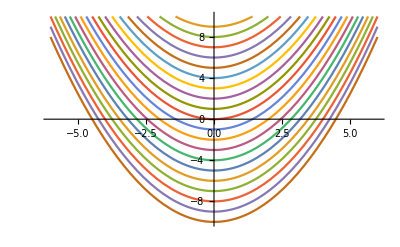

```mathematica
Rotate[Plot[Evaluate@Table[(t^2)/2-n,{n,-10,10,1}],{t,-6,6},PlotRange->{-10,10},Ticks->None],-Pi/2]
```

## Characteristic Curves (Variable coefficients case 2)

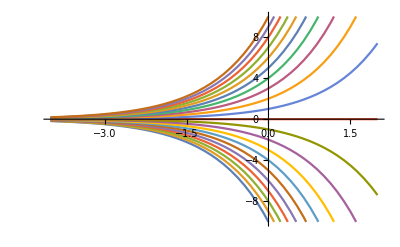

```mathematica
Plot[Evaluate@Table[n*Exp[t],{n,-10,10,1}],{t,-4,2},PlotRange->{-10,10}]
```

## Example Solutions to Semilinear Equation

```mathematica
Manipulate[Plot[1/(t+Exp[x*Exp[-t]]),{x,-20,20},PlotRange->{0,1}],{t,0,10}]
```

```mathematica
Manipulate[Plot[1/(t+Log[(x*Exp[-t])^2]),{x,-100,100},PlotRange->{0,10}],{t,1,10}]
```